The Mathematica^®Journal

# The Modular Group

## A Finitely Generated Group with Interesting Subgroups

Paul R. McCreary
Teri Jo Murphy
Christan Carter

The action of Möbius transformations with real coefficients preserves the hyperbolic metric in the upper half-plane model of the hyperbolic plane. The modular group is an interesting group of hyperbolic isometries generated by two Möbius transformations, namely, an order-two element g_2(z)=-1/z and an element of infinite order g_∞(z)=z+1. Viewing the action of the group elements on a model of the hyperbolic plane provides insight into the structure of hyperbolic 2-space. Animations provide dynamic illustrations of this action.

This article updates an earlier article [Reference].

## 1. Introduction

Transformations of spaces have long been objects of study. Many of the early examples of formal group theory were the transformations of spaces. Among the most important transformations are the isometries, those transformations that preserve lengths. Euclidean isometries are translations, rotations and reflections. The groups and subgroups of Euclidean isometries of the plane are so familiar to us that we may not think of them as revealing much about the space they transform. In hyperbolic space, however, light traveling or even a person traveling on a hyperbolic shortest-distance path tends to veer away from the boundary. Thus, the geometry is unusual enough so that viewing the actions of isometries of hyperbolic 2-space reveals some of the shape of that space. Two-dimensional hyperbolic space is referred to as the hyperbolic plane.

Here are graphic building blocks used for all of the animations.

```mathematica
RightTriangle=Module[{arc,center,start,end},
arc=Table[center+Cos[start+(end-start)n/21.]+I Sin[start+(end-start)n/21.],{n,21}];
Join[
arc/.{center->1,start->Pi,end->2Pi/3},
arc/.{center->0,start->Pi/3,end->Pi/2},
Table[I (1-n/21),{n,21-1}],
{.001I}
]
];
```

```mathematica
VerticalStrip=-1/RightTriangle;
```

```mathematica
LeftTriangle=-Conjugate@RightTriangle;
```

```mathematica
RightVerticalStrip=-1/LeftTriangle;
```

Figure NumberedFigure shows four cyan and white regions, each bounded by some combination of three arcs or rays. Any two adjacent regions make up a fundamental region. The two fundamental regions shown on either side of the y axis (each with one white and one cyan half) are related by the function -1/z, which is an inversion over the unit circle composed with a reflection in the y axis.

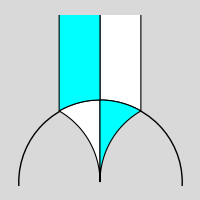

```mathematica
Graphics[{
Circle[],
EdgeForm[Black],
White,Polygon@*ReIm@LeftTriangle,Polygon@*ReIm@RightVerticalStrip,
Cyan,Polygon@*ReIm@RightTriangle,Polygon@*ReIm@VerticalStrip
},
PlotRange->{{-1,1},{0,2}},ImageSize->200{1,1},Background->LightGray]
```

Figure NumberedFigure. Two fundamental domains on either side of the y axis.

This article examines how elements of the modular group rearrange the triangular-shaped regions shown in Figure NumberedFigure. The curved paths are arcs of circles orthogonal to the x axis. Arcs on these circles are hyperbolic geodesics, that is, shortest-distance paths in hyperbolic 2-space. In Euclidean space, the shortest-distance paths lie on straight lines. In hyperbolic space, shortest paths lie on circles that intersect the boundary of the space at right angles. Hyperbolic distances are computed as if there is a penalty to pay for traveling near to the plane’s boundary. Thus, the shortest-distance paths between two points must bend away from the boundary.

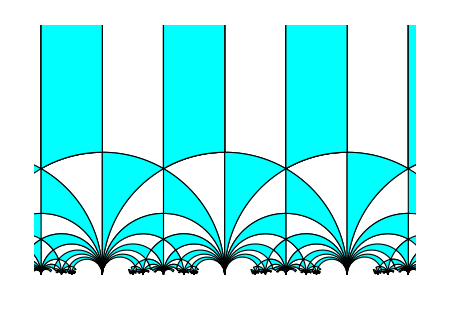

```mathematica
Graphics[{
Cyan,EdgeForm[Black],
Polygon@ReIm@Flatten[
Table[j-1/(k-1/(n+VerticalStrip)),{j,-2,2},{k,-4,4},{n,-2,3}],2
]
},
PlotRange->{{-1.5,1.505},{-.2,2}},ImageSize->450]
```

Figure NumberedFigure. The upper half-plane model of the hyperbolic plane.

In the animations that follow, it is instructive to focus on the action that a transformation takes on the family of circles that meet the x axis at right angles. The transformations that we consider, namely members of the modular group, preserve this family of circles. The circles in the family are shuffled onto different members in the family, but no new circles are created and none are taken away. One could say that in the context of hyperbolic geometry, the transformations preserve the family of all shortest-distance paths. Indeed this is an excellent thing for an isometry to do!

The context of this article can be found described in Chapter 2 of [Reference]. In this small text, one can find illustrations that inspired our animations. The formulas, which made coding the animations much simpler than one might expect, are given and justified in detail.

## 2. Möbius Transformations

First consider a class of functions known as Möbius transformations. These transformations are named after the same mathematician with whom we associate the one-sided, half-twisted Möbius band. Möbius transformations are defined by

f(z)=(a z+b)/(c z+d), a,b,c,d ∈ℂ,a d-b c≠0.

Here ℂ stands for the complex numbers. Over the reals, a Möbius transformation f(z)=(a z+b)/(c z+d) with real coefficients falls into one of two categories: either c=0, and the graph is a straight line, or c≠0, and the graph is a hyperbola. A representation of this latter type of function is shown in Figure NumberedFigure.

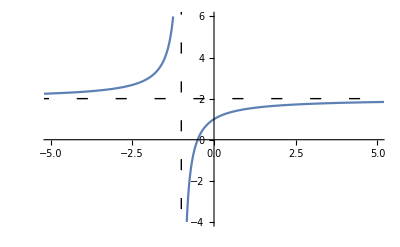

```mathematica
Show[
Plot[(2 x+1)/(x+1),{x,-10,10},PlotRange->{{-5,5},{-4,6}}],
Graphics[{Dashing[{.02,.05}],Line[{{-50,2},{50,2}}],Line[{{-1,-50},{-1,50}}]}],PlotRange->{{-5,5},{-4,6}}
]
```

Figure NumberedFigure. Graph of f(x)=(2x+1)/(x+1) shown with dashed asymptotes.

Our purpose is to investigate how Möbius transformations stretch and twist regions in the extended complex plane. The complex plane is the usual Euclidean plane with each point identified as a complex number—namely, (x,y)=x+i y. The extended complex plane is formed from the complex plane by adding the point at infinity. A Möbius transformation is one-to-one (injective) on the extended complex plane ℂ^*=ℂ∪{∞}.

When a Möbius transformation F acts on a complex number, F(x+i y)=u+i v, we may view the action as moving the point (x,y) to the point (u,v). Importantly, a Möbius transformation maps the set S of circles and lines in ℂ^* back to S in ℂ^*. A comprehensive proof of this fact may be found in most elementary texts on complex variables, for example, in [Reference], p. 158.

The figures of our animations live in the extended complex plane. Each point of a figure, taken as a complex number, is acted on by the Möbius transformations. These transformations spin hyperbolic 2-space about a fixed point or shift the space in one direction or another.

## 3. The Modular Group and Hyperbolic Space

The modular group M is a special class of Möbius transformations:

M:={f(z)=(a z+b)/(c z+d)|a,b,c,d∈ℤ,a d-b c=1}.

That is, if f∈M, the coefficients of f are integers and the coefficient matrix (a | b
c | d) has determinant equal to one.

What is a group? Recall that a group is a set G together with a binary operation satisfying certain properties: (1) the set G must be closed under the operation; (2) the operation must be associative; and (3) there must be an identity element for the operation, and all inverses of elements in G must themselves be elements of G. The proof that the modular group is, in fact, a group under the operation of function composition is a standard exercise in a course on complex analysis. (See, for example, [Reference], p. 277–278.)

We take as established that the elements of the modular group do indeed form a group and investigate some of the interesting subgroups.

### Fundamental Regions

One of our main goals is to investigate how the elements of the modular group act on fundamental regions. That is to say, how the regions are stretched and bent when we view them as Euclidean objects. As hyperbolic objects, the regions are all carbon copies of each other, in much the same way that the squares on a checkerboard are all identical in ordinary Euclidean geometry.

In general, a group of one-to-one transformations acting on a topological space partitions that space into fundamental regions. For a collection of sets {U_i} to be a collection of fundamental regions, certain properties must hold. First and foremost, the U_i must be pairwise disjoint. Second, given any transformation f in the group other than the identity, U_i and f(U_i) are disjoint. Finally, given any two regions U_i and U_j, there exists some transformation f such that f(U_i)=U_j.

Generally, in order to cover the entire space without overlapping, each fundamental region must contain some but not all of its boundary points. This technicality is set aside for the purposes of this article.

In fact, in this article we relax the definition to include all of the boundary points for a particular fundamental region. Thus, adjacent fundamental regions can only overlap on their boundaries. The essential feature remains that there is no area in the intersection of adjacent regions.

A group of transformations does not necessarily yield a unique partition of the space into fundamental regions. Thus, the fundamental regions we view are merely representative fundamental regions.

Figure NumberedFigure shows a fundamental region of the modular group with some parts highlighted.

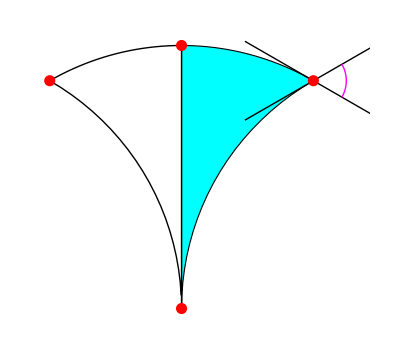

```mathematica
Module[{
(* vertex with tangents *) 
v={1/2,Sqrt[3]/2},

(* tangent directions *) 
d1=.3{Cos[Pi/6],Sin[Pi/6]},
d2=.3{Cos[-Pi/6],Sin[-Pi/6]}
},
Graphics[
{
EdgeForm[Black],Cyan,
Polygon@ReIm@RightTriangle,

Black,
(* tangent lines *)
 Line[{v+d1,v-d1}],
Line[{v+d2,v-d2}],

Line@ReIm@LeftTriangle,

Magenta,
Circle[v,1/8,{-Pi/6,Pi/6}],
Red,PointSize[.02],
Point[{{0,1},{-1,1}v,{0,0},v}]
}, 
PlotRange->{{-.55,.69},{-.05,1.05}}
]
]
```

Figure NumberedFigure. A fundamental region with vertices marked and a pair of tangents.

Each fundamental region contains four vertices that can be fixed by elements of the modular group. (A point f is fixed by f if f(p)=p.) Tangents are drawn at one vertex; the angle is 60 degrees. The vertex at the top has a straight, 180 degree angle. The vertex at the bottom has a zero degree angle because the tangents to the intersecting arcs coincide there. Any hyperbolic polygon with a vertex on the boundary of the space (the x axis in this case of the upper half-plane) has a zero degree angle at that vertex. The corresponding four angles in each fundamental region have the same measures as those indicated here. Each vertex can be fixed by some element in the modular group. Further, each fundamental region can be mapped onto any other fundamental region by an element of the modular group.

A classic view of the matter is to see the upper half-plane as tessellated (or tiled) by triangular-shaped regions, as in Figure NumberedFigure. A checkerboard tessellation of the Euclidean plane can be constructed by sliding copies of a square to the left, right, up and down. Eventually, the plane is covered with square tiles. The modular group tessellates the hyperbolic plane in an analogous way. The elements of the group move copies of a fundamental region until triangular-shaped tiles cover the upper half-plane model of the hyperbolic plane. Of course, these tiles do not appear to be identical to our eyes, trained to match shapes and lengths in Euclidean geometry. However, the triangular-shaped tiles are all identical if measured using the hyperbolic metric. In the tiling process, all areas in the upper half-plane are covered by tiles and no two tiles have any overlapping area. In fact, this procedure is precisely how the hyperbolic plane illustration was constructed. The boundary points for a single fundamental region were acted on by function elements of the modular group, and the resulting points were drawn as a boundary line in the illustration.

It helps to note that each transformation in M has at least one fixed point. Some transformations in M have two fixed points. Only the identity map has more than two. In the illustrations that follow, we observe the placement of fixed points and the way transformations map fundamental regions near them.

### Hyperbolic Lengths

The hyperbolic metric is a rather curious metric that challenges our notion of distance. Under the hyperbolic metric in the upper half-plane, the shortest distance between two points is along a vertical line or an arc of a circle perpendicular to the boundary (the real axis). For example, the shortest hyperbolic path between the points z=i and z=1+i is the top arc of the circle {z:|z-1/2|=(√5)/2}, which passes through both points and is perpendicular to the real axis (Figure NumberedFigure).

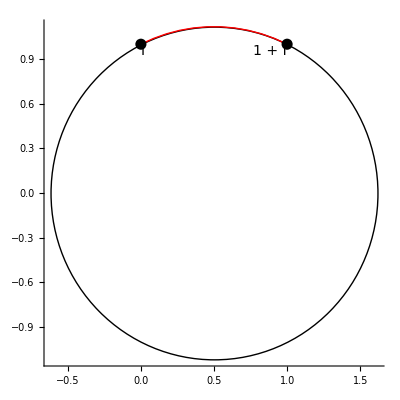

```mathematica
Show[
Graphics[
{
Circle[{.5,0},Sqrt[5/4]],
Text[Style["i",Italic,14],{0,1},{-7,2}],Text[Style[Row[{1," + ",Style["i",Italic]}],14],{1,1},{1.5,2}],
Red,Circle[{.5,0},Sqrt[5/4],{ArcTan[2],Pi-ArcTan[2]}],
RGBColor[0,0,0],PointSize[.02],Point[{{0,1},{1,1}}],PlotRange->{{-.7,1.7},{-1.2,1.2}}
}
],Axes->True
]
```

Figure NumberedFigure. The shortest hyperbolic path between the points i and 1+i.

Without discussing precisely how hyperbolic lengths and areas are measured, we state that every image under a transformation in the modular group is congruent to every other image under the hyperbolic metric. Thus, all of our fundamental regions shown in the animations are actually the same size in the hyperbolic metric. For a discussion on hyperbolic metrics, [Reference] is a good place to start.

## 4. Structure of the Modular Group

We structure our investigation of the modular group by considering four cyclic subgroups. Recall that a cyclic subgroup can be generated by computing all powers of a single group element. The four cyclic subgroups we present are representative of the four possible types of subgroups found in the modular group.

### Four Examples of Cyclic Subgroups

#### ⟨g_2⟩

For the first subgroup, consider the function g_2(z)=-1/z; it is a Möbius transformation with coefficients a=0, b=-1,c=1, d=0 and coefficient matrix (0 | -1
1 | 0). The subscript indicates that g_2 is of order two in M; that is, g_2(g_2(z))=z, and so g_2 is its own inverse. In this case, g_2 generates a subgroup with only two elements, namely M_2=⟨g_2⟩={z,-1/z}.

In this article, we adopt the standard notation that angular parentheses ⟨ ⟩ indicate the set of elements generated by taking products from the elements enclosed by the parentheses. Curly braces { }, on the other hand, enclose the delineated list of elements in a set.

```mathematica
g2[z_]:=-1/z
```

The Möbius transformation ρ, its inverse σ and the function R2 are used for the motion in Figure NumberedFigure.

```mathematica
ρ[z_]:=(z-I)/(z+I)
```

```mathematica
σ[z_]:=(z I+I)/(-z+1)
```

```mathematica
R2[F_,t_]:=Table[ReIm@Table[σ[Exp[2 Pi I t] ρ@F[[j]]],{j,Length[F]}][[i]],{i,2}]
```

```mathematica
Manipulate[
Graphics[
{
EdgeForm[Black],
LightGray,
Line@Flatten[Join[
{Table[ReIm[n-1/RightTriangle],{n,-2,2}]},
Table[ReIm[m-1/Table[n-1/RightTriangle,{n,-2,2}]],{m,-2,2}]
],1],
(* background figures *)

Table[{
{Lighter@Red,Darker@Green}[[n]],
Line[R2[{LeftTriangle,-1/LeftTriangle},t6][[n]]],
Polygon[R2[{RightTriangle,-1/RightTriangle},t6][[n]]]
},{n,2}]
(* pinweel arms *)
},
PlotRange->{{-1.5,1.5},{-.1,3}},Axes->True,Ticks->None,ImageSize->400],
{{t6,0,"rotation "},0,1,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. Action of the order-two element g_2(z)=-1/z.

The Manipulate depicts the way in which g_2 maps the two fundamental regions shown in Figure NumberedFigure onto one another. In fact, the action of g_2 on the fundamental regions is to hyperbolically rotate them 180° onto each other about the central fixed point z=i. The actual mapping is performed instantaneously without rotation. In particular, only the first, middle and final frames contain illustrations of fundamental regions. However, the sequence of intermediate mappings illustrates through animation the mapping properties of g_2. In a later section, we discuss how the functions illustrated were broken into a composition of functions so that the hyperbolic nature of their motion was made continuous.

This example highlights the fact that vertical lines are paths of least distance in the upper half-plane model of the hyperbolic plane. Indeed, it is usual to view straight lines as circles that have radii with infinite length and that pass through the point at infinity. With this bending of the definition of a circle, a vertical line has all the characteristics required of a geodesic in the hyperbolic plane. Like the circles, a vertical line is perpendicular to the x axis, which is the boundary of the upper half-plane model of the hyperbolic plane. A vertical line is the limit of a sequence of geodesic circles.

#### ⟨g_∞⟩

The second example (see Figure NumberedFigure) is a subgroup of infinite order generated by the linear shift (or translation) g_∞(z)=z+1; it is a Möbius transformation with a=1, b=1,c=0, d=1 and matrix (1 | 1
0 | 1). The function g_∞ has infinite order because g_∞^n(z)=z+n, and no point of ℂ ever returns to its original position no matter how many times g_∞ is applied, though g_∞(∞)=∞ in the extended plane. The subgroup produced by taking all powers of g_∞ and its inverse (g_∞)^-1(z)=z-1 is denoted as M_∞=⟨g_∞⟩={…,z-2,z-1,z,z+1,z+2,…}.

Every point in the plane shifts one unit to the right under the action of g_∞. The infinite half-strips in the following Manipulate are images of each other under powers of g_∞. For contrast, we also provide images of these infinite half-strip regions under the map g_2(z)=-1/z. These images are bunched in a flower-like arrangement attached to the real axis at the origin. As the blue infinite regions are pushed from left to right, their magenta images echo their motion in a counterclockwise direction. These two actions are not produced by a single transformation. The two transformations that cause these actions are closely related to each other as algebraic conjugates, but more on that in a later section.

```mathematica
Manipulate[
Graphics[
{
LightGray,
Line[Flatten[Join[
{Table[ReIm[n-1/RightTriangle],{n,-2,3}]},
Table[ReIm[m-1/Table[n-1/RightTriangle,{n,-2,2}]],{m,-2,2}]
],1]],
(* background figures *)

Lighter@Blue,
Line@ReIm[8 (t7-1/2)+Table[n-1/LeftTriangle,{n,-1,1}]],
(* lines on vertical fundamental region *)

EdgeForm[Black],
Polygon@ReIm[8 (t7-1/2)+Table[n-1/RightTriangle,{n,-1,1}]],
(* polygons on vertical fundamental region *)

Lighter@Magenta,
Line@ReIm[-1/(8 (t7-1/2)-1/Table[-1/(n-1/LeftTriangle),{n,-1,1}])],
Polygon@ReIm[-1/(8 (t7-1/2)-1/Table[-1/(n-1/RightTriangle),{n,-1,1}])]
(* polygons on fundamental region at origin *)
},
PlotRange->{{-2.5,2.5},{-.1,2.3}},Axes->True,Ticks->None,ImageSize->1.2{400,200}
],
{{t7,.5,"translation "},0,1,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. This animation shows copies of fundamental regions moving back and forth, with corresponding regions anchored at the origin.

The hyperbolic isometry g_∞ is notable among the elements of the modular group because it is also a Euclidean isometry. Under the hyperbolic metric, the magenta regions are each congruent to the half-strip regions in blue.

#### ⟨g_3⟩

The third cyclic subgroup of M that we consider is generated by the composition of the first two functions g_∞ and g_2: define g_3(x)=g_∞∘g_2(z)=(z-1)/z. The subgroup generated by this element is denoted M_3=⟨g_3⟩={z,(z-1)/z,-1/(z-1)}, a subgroup of order 3.

```mathematica
g3[z_]:=(z-1)/z
```

Here is the fixed point of g_3.

```mathematica
τ=1/2(1+I √3);
```

```mathematica
g3[τ]==τ//Simplify
```

True

Define μ and its inverse ν.

```mathematica
μ[z_]:=(z-τ)/(z-Conjugate[τ])
```

```mathematica
ν[z_]:=(- Conjugate[τ]z+τ)/(-z+1)
```

In Figure NumberedFigure, the function μ moves the fixed point τ to the origin and ν moves it back.

```mathematica
μ[τ]//Simplify
```

0

```mathematica
ν[0]
```

1/2 (1+ⅈ √3)

The function R3 is an order-three hyperbolic rotation made continuous; it is used in Figures NumberedFigure and NumberedFigure.

```mathematica
R3[F_,t_]:=Table[ReIm@Table[ν[μ[F[[j]]] Exp[2/3 Pi I t]],{j,Length[F]}][[i]],{i,3}]
```

```mathematica
Manipulate[
Graphics[
{
EdgeForm[Black],
LightGray,
Line@Flatten[Join[
{Table[ReIm[n-1/RightTriangle],{n,-1,2}]},
Table[ReIm[m-1/Table[n-1/RightTriangle,{n,-1,2}]],{m,-1,2}]
],1],
(* background figures *)

Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line@R3[{LeftTriangle,1-1/LeftTriangle,1-1/(1-1/LeftTriangle)},t8][[m]],
Polygon@R3[{RightTriangle,1-1/RightTriangle,1-1/(1-1/RightTriangle)},t8][[m]]},
{m,1,3}]
(* arms of pinwheel *)
},
PlotRange->{{-1,2},{-.1,3}},Axes->True,Ticks->None,ImageSize->400
],
{{t8,0,"rotation "},0,3,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. Action of the order-three element g_3(z)=(z-1)/z.

A red fundamental region and a green fundamental region are shown associated with the blue fundamental region attached to the origin in the animation’s first frame. We include these in order to provide a better orientation for the scene. Of special interest is how the point of the blue region on the x axis moves as the rotation takes place. The point begins at the origin and slides toward the right along the positive x axis. The blue lines of the cluster become vertical precisely when that point arrives at the point at infinity! The point continues by sliding along the negative x axis to arrive back at the origin. It is fair to say that the motion of a point as it passes through the origin is a “mirror image” of the motion of the point as it passes through the point at infinity. The function used here is a composition of Möbius transformations that is described and demonstrated in Figure NumberedFigure.

#### ⟨g_h⟩

The rotations we saw in the action of g_2 and g_3 are of orders two and three, respectively. That is to say, after the rotation is repeated a number of times, all points are back to their original positions. In contrast, the function g_∞ generates an infinite subgroup. When we iterate g_∞, the right shifts accumulate at the point at infinity. Points in the left half-plane get repelled by infinity, while points in the right half-plane get attracted to infinity. Of course, since all points in the left half-plane eventually map to points in the right half-plane, all points are, in some sense, simultaneously attracted to and repelled by infinity under the action of g_∞. Indeed, the point at infinity is the single fixed point for the action of g_∞.

The transformation g_h(z)=(2z+1)/(z+1) in the modular group generates an infinite subgroup M_h that differs from M_∞ in the sense that g_h has two distinct fixed points, an attractor and a repeller.

Define the well-known golden ratio ϕ; its reciprocal is 1/ϕ=1-ϕ.

```mathematica
ϕ=1/2(1+√5);
```

```mathematica
1/ϕ==ϕ-1
```

True

This defines g_h with fixed points ϕ and 1-ϕ.

```mathematica
gh[z_]:=(2z+1)/(z+1)
```

```mathematica
gh/@{ϕ,1-ϕ}//Simplify
```

{1/2 (1+√5),1/2 (1-√5)}

Define α to move the fixed points ϕ and 1-ϕ to infinity and zero, respectively.

```mathematica
α[z_]:=(z-(1-ϕ))/(z-ϕ)
```

```mathematica
α[ϕ]//Simplify//Quiet
```

ComplexInfinity

```mathematica
α[1-ϕ]//Simplify
```

0

Define β to be the inverse of α; β sends infinity back to ϕ and zero back to 1-ϕ.

```mathematica
β[z_]:=(-ϕ z+(1-ϕ))/(-z+1)
```

```mathematica
Limit[β[z],z->∞]
```

1/2 (1+√5)

```mathematica
β[0]//Simplify
```

1/2 (1-√5)

For Figure NumberedFigure, γ makes the hyperbolic translation continuous. The ratio α[1]/α[0] is the length of the hyperbolic translation.

```mathematica
γ[z_,e_]:=β[(α[1]/α[0])^e α[z]]
```

```mathematica
Manipulate[
Module[{topOfUnitCircle,MovingRegion},
topOfUnitCircle=Table[Cos[(2 π k)/114]+I Sin[(2 π k)/114],{k,0.,57}];
MovingRegion=Join[
Table[n+VerticalStrip,{n,-4,4}],
1-1/Table[n+VerticalStrip,{n,0,4}],
-1/Table[VerticalStrip+n,{n,-4,0}],
-2-1/Table[n+VerticalStrip,{n,0,4}]
];

Graphics[
{
Lighter@Gray,
Line@ReIm@Join[
Table[n+VerticalStrip,{n,-4,4}],
-1/Table[n+VerticalStrip,{n,-2,2}]
],
(* background figures *)

InfiniteLine[{{-1,0},{1,0}}],
Blue,Line@ReIm[γ[MovingRegion,t9]],
Red,Circle[{-1,0},1,{0,Pi}],
Darker@Green,Circle[{2,0},1,{0,Pi}],
Cyan,Line@ReIm@gh[topOfUnitCircle+2],
(* boundary circles *)

Cyan,Line@ReIm@γ[topOfUnitCircle+2,t9],
Darker@Green,Line@ReIm@γ[topOfUnitCircle-1,t9],
(* boundary of moving region *)


PointSize[.01],
Red,Point[{1-ϕ,0}],
Darker@Green,Point[{ϕ,0}]
(* fixed points *)
}, 
AspectRatio->Automatic,PlotRange->{{-4,4},{-.2,4}},ImageSize->500]
],

{{t9,0,"translate "},0,1,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. Action of the hyperbolic element g_h(z)=(2z+1)/(z+1).

The Manipulate depicts the action of g_h on fundamental regions in the plane. All points exterior to the red circle on the left are mapped to the interior of the green circle on the right. The animation begins with regions that lie exterior to the red and green circles. These regions are all mapped to the area between the green circle and smaller cyan circle. If the action of g_h were to be repeated, the regions would be mapped into the interior of increasingly small circles inside the smallest (cyan) circle shown. The attracting fixed point for g_h lies within these shrinking, nested circles.

The rotations and translations we have seen as examples are intimately related to Euclidean rotations and translations, as discussed in Section Section. The transformation g_h is related in a similar way to a Euclidean dilation, which turns a figure into a similar but not congruent image figure. A curious characteristic of hyperbolic space is that the distinction between similarity and congruence disappears. In the hyperbolic plane, it is enough for two figures to have the same angles to guarantee congruence. In marked contrast to Euclidean space, equal angles guarantee that corresponding side lengths are equal in the hyperbolic metric.

### Generators of M

The entire group M can be generated by the two functions g_2 and g_∞. In symbols, M=⟨g_2,g_∞⟩. Establishing this fact requires tools from linear algebra about which we make only a few brief comments. The group of 2×2 matrices with real number entries and with nonzero determinants is denoted by GL[2,ℝ]. This group has been studied extensively and much is known about it. Thus, there are great advantages for any group that can be represented as a subgroup of GL[2,ℝ]. While the modular group cannot be represented in exactly this way, it almost can be. For instance, the elements (1 | 2
1 | 3) and (-1 | -2
-1 | -3) are considered distinct in GL[2,ℝ]. On the other hand, the actions of the two associated Möbius transformations are identical, since (-z-2)/(-z-3)=(-(z+2))/(-(z+3))=(z+2)/(z+3). In general, for every element in the modular group, there are two associated elements in GL[2,ℝ].

A remarkable feature of Möbius transformations is that the group operation of compositions produces coefficients that are identical to the results of 2×2 matrix multiplication. To see this, consider the two Möbius transformations (a z+b)/(c z+d) and (e z+f)/(g z+h). First, multiply the associated 2×2 matrices.

(a | b
c | d).(e | f
g | h)=(a e+b g | a f+b h
c e+d g | c f+d h).

Second, carry out the composition of the two functions.

(a (e z+f)/(g z+h)+b)/(c (e z+f)/(g z+h)+d)=(a (e z+f) +b (g z+h))/(c (e z+f)+d (g z+h))=((a e+b g)z+(a f+b h))/((c e+d g)z+(c f+d h)).

The coefficients and the four matrix entries are the same!

In this way, the group operation of composition of functions in the modular group can be replaced with the group operation of matrix multiplication in GL[2,ℝ]. It is down this path we would travel if we were to present a complete proof of the claim that the modular group is generated by the two elements g_2 and g_∞.

A major part of this claim is that any element of M can be written as a composition of g_2 and g_∞. Consider the following examples of compositions.

g_∞∘g_2(z)=(z-1)/z.

g_∞∘g_∞∘g_2(z)=(2z-1)/z.

g_∞∘g_∞∘g_2∘g_∞∘g_∞∘g_2(z)=(3z-2)/(2z-1).

Each of these functions has a coefficient matrix with determinant equal to one. A worthy exercise for undergraduate mathematics students is to verify by direct computations that each equality holds for the indicated compositions.

## 5. Conjugate Subgroups

The four examples of cyclic subgroups outlined in Section Section give a complete description of the four types of subgroups possible in the modular group. Any subgroup of the modular group is conjugate to a subgroup generated by g_2, g_3, an iterate of g_∞ or an iterate of an element of the same type as g_h.

Recall that in a group G, a subgroup H is conjugate to a subgroup K if there exists an element g ϵ G such that the entire subgroup H can be generated by computing g k g^-1 for every k ϵ K. More compactly, we write H={g k g^-1|k ϵ K}, and even more compactly, H=g K g^-1.

Here we define the hyperbolic translation η that relates two order-three elements: g_3 and f.

```mathematica
η[z_]:=z/(z+1)
```

Consider a function f in the modular group that generates an order-three subgroup (Figure NumberedFigure).

```mathematica
f[F_,t_]:=Table[ReIm@Table[η[ν[μ[F[[j]]] Exp[2/3 Pi I t]]],{j,Length[F]}][[i]],{i,3}]
```

```mathematica
RotatingRegions=
{
Table[n+VerticalStrip,{n,0,2}],
Table[-1/(VerticalStrip+n)+1,{n,0,2}],
Table[-1/(VerticalStrip+n-1),{n,0,2}]
};
```

```mathematica
RotatingRegionsRight=
{
Table[RightVerticalStrip+n,{n,0,2}],
Table[-1/(RightVerticalStrip+n)+1,{n,0,2}],
Table[-1/(RightVerticalStrip+n-1),{n,0,2}]
};
```

```mathematica
Manipulate[
Graphics[
{
Lighter@Gray,Circle[{0,0},1],
EdgeForm[Black],
LightGray,
Line@Flatten[Join[
{Table[ReIm[n-1/RightTriangle],{n,-1,2}]},
Table[ReIm[m-1/Table[n-1/RightTriangle,{n,-1,2}]],{m,-1,2}]
],1],
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Polygon@f[RotatingRegions,t10][[n,2]]},{n,3}],
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Line@f[RotatingRegionsRight,t10][[n,2]]},{n,3}]
},PlotRange->{{-.6,1.5},{-.1,2}},ImageSize->2{200,200}
]
,

{{t10,0,"rotate "},0,3,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. The action of the order-three function f on a selection of fundamental regions.

We view side by side the actions of f on the right and η^-1 g_3 η on the left. For the figure on the left, first the function η moves the fixed point of f onto the fixed point of g_3. Then the function g_3 rotates the attached fundamental regions, as we have seen it do before, while at the same time the function f acts on the right-hand figure. Finally, the inverse of η returns the fixed point and associated regions to the original position, except that the fundamental regions have been rotated in the same way as those on the right. Thus, the final results are the same in both cases.

The function ζ is used for the continuous motion in Figure NumberedFigure.

```mathematica
ζ[z_,t_]:=(z+t-1)/(z+t)
```

```mathematica
graphics11[t_,table1_,table2_]:=Framed@Graphics[
{
EdgeForm[Black],
LightGray,
Line[Flatten[Join[
{Table[ReIm/@(-1/RightTriangle+n),{n,-1,2}]},
Table[ReIm/@(-1/Table[-1/RightTriangle+n,{n,-1,2}]+m),{m,-1,2}]
],1]],
table1,table2},PlotRange->{{-.6,1.5},{-.1,2}},ImageSize->{250,250}
]
```

```mathematica
Manipulate[
Grid[{
Which[
t11≤1/3,
{
graphics11[1-3t11,
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Polygon[ReIm/@ζ[RotatingRegions,1-3t11][[n,2]]]},{n,3}],
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Line[ReIm/@ζ[RotatingRegionsRight,1-3t11][[n,2]]]},{n,3}]
],
Spacer[10],
graphics11[1,
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Polygon[ReIm/@ζ[RotatingRegions,1][[n,2]]]},{n,3}],
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Line[ReIm/@ζ[RotatingRegionsRight,1][[n,2]]]},{n,3}]
]
},
1/3<t11≤2/3,
{
graphics11[3(t11-1/3),
Table[{{Darker@Green,Lighter@Red,Lighter@Blue}[[n]],Polygon[R3[RotatingRegions,3(t11-1/3-del)][[n,2]]]},{n,3}],
Table[{{Darker@Green,Lighter@Red,Lighter@Blue}[[n]],Line[R3[RotatingRegionsRight,3(t11-1/3-del)][[n,2]]]},{n,3}]
],
Spacer[10],
graphics11[3(t11-1/3),
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Polygon[f[RotatingRegions,3(t11-1/3-del)][[n,2]]]},{n,3}],
Table[{{Lighter@Red,Lighter@Blue,Darker@Green}[[n]],Line[f[RotatingRegionsRight,3(t11-1/3-del)][[n,2]]]},{n,3}]
]
},
t11>2/3,
{
graphics11[3(t11-2/3),
Table[{{Lighter@Blue,Darker@Green,Lighter@Red}[[n]],Polygon[ReIm/@ζ[RotatingRegions,3(t11-2/3-2del)][[n,2]]]},{n,3}],
Table[{{Lighter@Blue,Darker@Green,Lighter@Red}[[n]],Line[ReIm/@ζ[RotatingRegionsRight,3(t11-2/3-2del)][[n,2]]]},{n,3}]
],
Spacer[10],
graphics11[1,
Table[{{Lighter@Blue,Darker@Green,Lighter@Red}[[n]],Polygon[ReIm/@ζ[RotatingRegions,1][[n,2]]]},{n,3}],
Table[{{Lighter@Blue,Darker@Green,Lighter@Red}[[n]],Line[ReIm/@ζ[RotatingRegionsRight,1][[n,2]]]},{n,3}]
]
}
]
}],
{{t11,0,"transform "},0,1,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. The action of η^-1 g_3 η and f.

This animation demonstrates what it means for two functions to be conjugate equivalent.

## 6. Coding Considerations

All functions in the modular group are abruptly discontinuous; that is, their actions move triangular regions onto other regions all in one jump. The facility to produce transformations that seem continuous is due to the following.

Every element of the modular group is conjugate equivalent to one of three Euclidean transformations, namely a rotation about the origin, a scaling from the origin or a rigid translation of the entire plane ([Reference], pp. 12–20).

These Euclidean transformations have very simple continuous forms:

Rotation: ℛ_θ(z)=e^iθ z, θ∈[0,2π).

Scaling: 𝒮_k(z)=k z, k∈(0,∞).

Translation: 𝒯_a(z)=z+a, a∈ℂ.

The left-hand side of Figure NumberedFigure shows the fixed point of g_3 translated to the origin. Following this transformation, all circles that passed through the original fixed point become straight lines passing through the origin. A Euclidean rotation about the origin accomplishes the desired rearrangement of the regions. Finally, translating the fixed points back to their original positions maps the fundamental regions to their proper, final positions. We see that the final results are the same for the right and left animations.

Indeed, each frame in the right-hand animation was computed by composing the functions that are explicitly portrayed in the left-hand animation.

```mathematica
generalLFT[z_,z1_,w1_,z2_,w2_,z3_]:=N[-(-w1+w2) (w2/(w1-w2)+((z-z2) (z1-z3))/((z1-z2) (z-z3)))]
```

```mathematica
(* z3-> Infinity *)
moveToOrigin[z_,t_]:=generalLFT[z,.5+Sqrt[3]/2 (2-t) I,0,.5-Sqrt[3]/2 (1-t) I,-(1+2.5 (1-t)) I,.5-(Sqrt[3]/2+2Sqrt[3]/2 (1-t)) I]-generalLFT[.5+I Sqrt[3]/2,.5+(Sqrt[3]/2+Sqrt[3]/2 (1-t)) I,0,.5-Sqrt[3]/2 (1-t) I,-(1+2.5 (1-t)) I,.5-(Sqrt[3]/2+2Sqrt[3]/2 (1-t)) I]+(.5+I Sqrt[3]/2) (1-t)
```

```mathematica
graphics12[table_]:=Framed[Graphics[
{
LightGray,
Circle[{0,0},1],Line[{{-10,0},{10,0}}]
(* background figures *),
EdgeForm[Black],
table
},
PlotRange->{{-1.5,1.5},{-1,2}},ImageSize->{250,250}]]
```

```mathematica
Manipulate[
Which[
t12<0,
Grid[{
{
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1}[[m]])],
Polygon[ReIm/@({RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1}[[m]])]},
{m,1,3}]
(* arms of pinwheel *)
],
Spacer[10],
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1}[[m]])],
Polygon[ReIm/@({RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1}[[m]])]},
{m,1,3}]
]
}
}],
0≤t12&&t12≤1/3,
Grid[{
{
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@(moveToOrigin[{LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1},3t12][[m]])],
Polygon[ReIm/@(moveToOrigin[{RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1},3t12][[m]])]},
{m,1,3}]
],
Spacer[10],
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1}[[m]])],
Polygon[ReIm/@({RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1}[[m]])]},
{m,1,3}]
]
}
}],
t12>1/3 && t12≤2/3,
Grid[{
{
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@(E^(I(t12-1/3) 2Pi)moveToOrigin[{LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1},1][[m]])],
Polygon[ReIm/@(E^(I(t12-1/3) 2Pi)moveToOrigin[{RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1},1][[m]])]},
{m,1,3}]
],
Spacer[10],
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[R3[{LeftTriangle,-1/LeftTriangle+1,-1/(-1/LeftTriangle+1)+1},3(t12-1/3) ][[m]]],
Polygon[R3[{RightTriangle,-1/RightTriangle+1,-1/(-1/RightTriangle+1)+1},3(t12-1/3) ][[m]]]},
{m,1,3}]
]
}
}],
t12>2/3 && t12<=1,
Grid[{
{
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@(moveToOrigin[{-1/(-1/LeftTriangle+1)+1,LeftTriangle,-1/LeftTriangle+1},1-3(t12-2/3)][[m]])],
Polygon[ReIm/@(moveToOrigin[{-1/(-1/RightTriangle+1)+1,RightTriangle,-1/RightTriangle+1},1-3(t12-2/3)][[m]])]},
{m,1,3}]
],
Spacer[10],
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({-1/(-1/LeftTriangle+1)+1,LeftTriangle,-1/LeftTriangle+1}[[m]])],
Polygon[ReIm/@({-1/(-1/RightTriangle+1)+1,RightTriangle,-1/RightTriangle+1}[[m]])]},
{m,1,3}]
]
}
}],
t12>1,
Grid[{
{
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({-1/(-1/LeftTriangle+1)+1,LeftTriangle,-1/LeftTriangle+1}[[m]])],
Polygon[ReIm/@({-1/(-1/RightTriangle+1)+1,RightTriangle,-1/RightTriangle+1}[[m]])]},
{m,1,3}]
],
Spacer[10],
graphics12[
Table[{
{Lighter@Blue,Darker@Green,Lighter@Red}[[m]],Line[ReIm/@({-1/(-1/LeftTriangle+1)+1,LeftTriangle,-1/LeftTriangle+1}[[m]])],
Polygon[ReIm/@({-1/(-1/RightTriangle+1)+1,RightTriangle,-1/RightTriangle+1}[[m]])]},
{m,1,3}]
]
}
}]
],
{{t12,-0.01,"composition rotation "},-0.01,1.01,Appearance->"Labeled"},
SaveDefinitions->True
]
```

Figure NumberedFigure. Conjugation with rotation of 120°.

In this way, the action of the hyperbolic motions can be animated as continuous because the Euclidean rotations, translations and dilations can all be coded as continuous functions.

## References

P. McCreary, T. J. Murphy and C. Carter, “The Modular Group,” The Mathematica Journal, 9(3), 2005. www.mathematica-journal.com/issue/v9i3.

L. Ford, Automorphic Functions, New York: McGraw-Hill, 1929.

N. Levinson and R. M. Redheffer, Complex Variables, San Francisco: Holden-Day, 1970.

E. W. Weisstein. “Hyperbolic Metric” from Wolfram MathWorld—A Wolfram Web Resource. mathworld.wolfram.com/HyperbolicMetric.html.

P. R. McCreary, T. J. Murphy and C. Carter, “The Modular Group,” The Mathematica Journal, 2018. doi:10.3888/tmj.20–3.

About the Authors

Paul R. McCreary
The Evergreen State College-Tacoma
Tacoma, WA
mccrearp@evergreen.edu

Teri Jo Murphy
Department of Mathematics & Statistics
Northern Kentucky University
Highland Heights, KY

Christan Carter
Department of Mathematics 
Xavier University of Louisiana
New Orleans, LA